TotalModelling::shdw: Symbol TotalModelling appears in multiple contexts {EqualSphereMoveModellingLib`,Global`}; definitions in context EqualSphereMoveModellingLib` may shadow or be shadowed by other definitions.

Move by MRI: {0,-9,-15,-9.6,-5}

Diastole and sistole contour

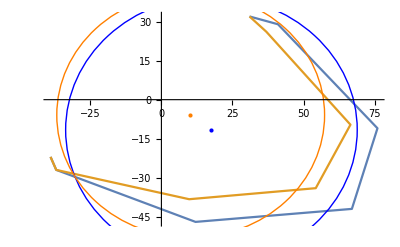

Center sphere moving = {-7.47491,5.87942}

F::HCoutourDxDyForEachChannel::Full verbouse mode

F::HCoutourDxDyForEachChannel::points of channel on contour{{-37,-27},{12,-47},{67,-42},{76,-11},{41,29}}

Function

Param model: <|a→{0.04,0.04,0.05,0.05,0.04},b→{0.02,0.02,0.025,0.025,0.02},R→{0.037,0.032,0.047,0.039,0.037},h→{0.031,0.025,0.024,0.025,0.03},x→{0,0,0,0,0},y→{0.027,0.04,0.015,0.039,0.027},hFat→{0.007},flSize→{0.06,0.03}|>

Exp data: <|dZRad→{0.04,0.055,0.11,0.083,0.076},zBase→{70,67,58,67,76},flDZ→0.1,flBase→79|>

DxDy: {{-2.57243,9.15557},{7.54584,5.7881},{9.45616,1.01137},{8.24002,4.74805},{2.70748,9.11655}}

Radial Move : {0.0027,0.002,0.0014,0.0012,0.0026}

Contours by impedance evaluation.

Diastole contour: {{-39,-22},{-37,-27},{12,-47},{67,-42},{76,-11},{41,29},{31,32}}

Sistole contour:{{-39,-22},{-34.819,-25.4084},{11.5052,-45.0622},{65.8138,-41.2564},{74.8124,-10.8281},{38.8773,27.4986},{31,32}}

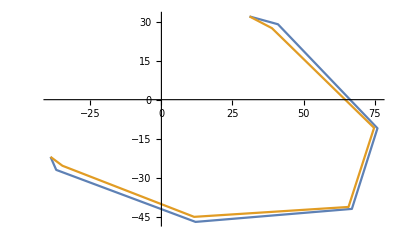

Volume calculation

Diastole volume: 622

Sistole volume:514

54.

```mathematica
Get["EqualSphereMoveModellingLib.m"]
RadialEvaluation["Artem","None", "Use_Contour","FirstLayer", True]
```

```mathematica
ivan
alex
artem
```

{{{44.5,78.,14.},{44.5,78.,21.}},{{38.5,82.,23.},{38.5,82.,44.5}}}

{{{19.5,79.5,33.5},{19.5,79.5,17.5}},{{18.5,61.,55.5},{18.5,61.,53.5}}}

{{{14.5,54.,-44.5},{14.5,54.,-2.5}},{{-3.,88.5,-14.},{-3.,88.5,55.}}}

### Расчет объема (без подробностей)

```mathematica
Get["EqualSphereMoveModellingLib.m"]
ivan = TotalModelling["Ivan", False];
alex = TotalModelling["Alex", False];
artem = TotalModelling["Artem", False];
```

None  Use_Contour  None

Vol = 44.5

None  Use_Contour  FirstLayer

Vol = 78.

None  Use_Contour  FirstLayer_CenterMove

verb Null

Vol = 14.

None  Use_Contour_Radius  None

Vol = 44.5

None  Use_Contour_Radius  FirstLayer

Vol = 78.

None  Use_Contour_Radius  FirstLayer_CenterMove

verb Null

Vol = 21.

ValveMove  Use_Contour  None

Vol = 38.5

ValveMove  Use_Contour  FirstLayer

Vol = 82.

ValveMove  Use_Contour  FirstLayer_CenterMove

verb Null

Vol = 23.

ValveMove  Use_Contour_Radius  None

Vol = 38.5

ValveMove  Use_Contour_Radius  FirstLayer

Vol = 82.

ValveMove  Use_Contour_Radius  FirstLayer_CenterMove

verb Null

Vol = 44.5

None  Use_Contour  None

Vol = 19.

None  Use_Contour  FirstLayer

Vol = 75.

None  Use_Contour  FirstLayer_CenterMove

verb Null

Vol = 26.5

None  Use_Contour_Radius  None

RegionCentroid::nmet: Unable to compute the centroid of region Polygon[{{-39,-22},{-40,-10},{-16,-63},{42,-63},{65,-40},{42,10},{35,13}}].

Vol = 19.

None  Use_Contour_Radius  FirstLayer

RegionCentroid::nmet: Unable to compute the centroid of region Polygon[{{-39,-22},{-40,-10},{-16,-63},{42,-63},{65,-40},{42,10},{35,13}}].

Vol = 75.

None  Use_Contour_Radius  FirstLayer_CenterMove

RegionCentroid::nmet: Unable to compute the centroid of region Polygon[{{-39,-22},{-40,-10},{-16,-63},{42,-63},{65,-40},{42,10},{35,13}}].

General::stop: Further output of RegionCentroid::nmet will be suppressed during this calculation.

verb Null

Vol = 14.

ValveMove  Use_Contour  None

Vol = 10.

ValveMove  Use_Contour  FirstLayer

Vol = 61.5

ValveMove  Use_Contour  FirstLayer_CenterMove

verb Null

Vol = 30.5

ValveMove  Use_Contour_Radius  None

Vol = 10.

ValveMove  Use_Contour_Radius  FirstLayer

Vol = 61.5

ValveMove  Use_Contour_Radius  FirstLayer_CenterMove

verb Null

Vol = 39.5

None  Use_Contour  None

Vol = 14.5

None  Use_Contour  FirstLayer

Vol = 54.

None  Use_Contour  FirstLayer_CenterMove

verb Null

Vol = -44.5

None  Use_Contour_Radius  None

Vol = 14.5

None  Use_Contour_Radius  FirstLayer

Vol = 54.

None  Use_Contour_Radius  FirstLayer_CenterMove

verb Null

Vol = -2.5

ValveMove  Use_Contour  None

Vol = -3.

ValveMove  Use_Contour  FirstLayer

Vol = 88.5

ValveMove  Use_Contour  FirstLayer_CenterMove

verb Null

Vol = -14.

ValveMove  Use_Contour_Radius  None

Vol = -3.

ValveMove  Use_Contour_Radius  FirstLayer

Vol = 88.5

ValveMove  Use_Contour_Radius  FirstLayer_CenterMove

verb Null

Vol = 55.

### Расчет объема (подробно)

#### Ivan

None  Use_Contour  None

Move by MRI: {-7.2,-15.93,-14.2,-12.25,-13.68}

Diastole and sistole contour

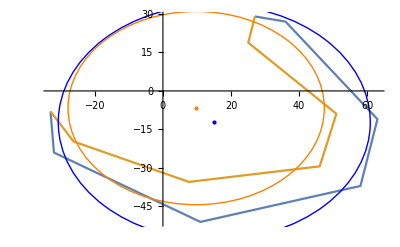

Center sphere moving = {-5.31667,5.54347}

F::HCoutourDxDyForEachChannel::Full verbouse mode

F::HCoutourDxDyForEachChannel::points of channel on contour{{-32,-24},{11,-51},{58,-37},{63,-11},{36,27}}

Function

Param model: <|a→{0.04,0.04,0.05,0.05,0.04},b→{0.02,0.02,0.025,0.025,0.02},R→{0.051,0.04,0.042,0.042,0.041},h→{0.03,0.019,0.022,0.021,0.03},x→{0,0,0,0,0},y→{0.047,0.026,0.035,0.048,0.025},hFat→{0.},flSize→{0.06,0.03}|>

Exp data: <|dZRad→{0.057,0.11,0.13,0.067,0.115},zBase→{35,33,33,30,42},flDZ→0.045,flBase→35|>

DxDy: {{-0.927256,7.62478},{6.53982,4.02839},{7.46366,1.8141},{6.19092,4.54638},{0.927256,7.62478}}

Radial Move : {0.0037,0.0022,0.0021,0.0014,0.0037}

Contours by impedance evaluation.

Diastole contour: {{-33,-8},{-32,-24},{11,-51},{58,-37},{63,-11},{36,27},{27,29}}

Sistole contour:{{-33,-8},{-29.04,-21.78},{10.5362,-48.8495},{56.2296,-35.8706},{61.6209,-10.7592},{33.04,24.78},{27,29}}

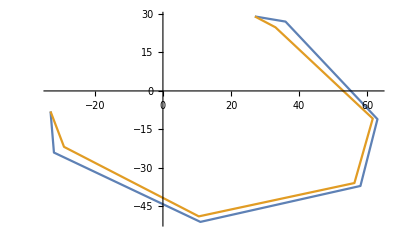

Volume calculation

Diastole volume: 485

Sistole volume:396

Vol = 44.5

None  Use_Contour  FirstLayer

Move by MRI: {-7.2,-15.93,-14.2,-12.25,-13.68}

Diastole and sistole contour

-Graphics-

Center sphere moving = {-5.31667,5.54347}

F::HCoutourDxDyForEachChannel::Full verbouse mode

F::HCoutourDxDyForEachChannel::points of channel on contour{{-32,-24},{11,-51},{58,-37},{63,-11},{36,27}}

Function

Param model: <|a→{0.04,0.04,0.05,0.05,0.04},b→{0.02,0.02,0.025,0.025,0.02},R→{0.051,0.04,0.042,0.042,0.041},h→{0.03,0.019,0.022,0.021,0.03},x→{0,0,0,0,0},y→{0.047,0.026,0.035,0.048,0.025},hFat→{0.},flSize→{0.06,0.03}|>

Exp data: <|dZRad→{0.057,0.11,0.13,0.067,0.115},zBase→{35,33,33,30,42},flDZ→0.045,flBase→35|>

DxDy: {{-0.927256,7.62478},{6.53982,4.02839},{7.46366,1.8141},{6.19092,4.54638},{0.927256,7.62478}}

Radial Move : {0.0078,0.0034,0.0029,0.0024,0.0058}

Contours by impedance evaluation.

Diastole contour: {{-33,-8},{-32,-24},{11,-51},{58,-37},{63,-11},{36,27},{27,29}}

Sistole contour:{{-33,-8},{-25.76,-19.32},{10.2832,-47.6764},{55.5551,-35.4403},{60.6358,-10.5872},{31.36,23.52},{27,29}}

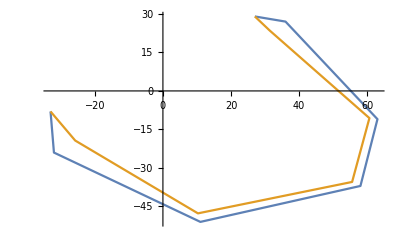

Volume calculation

Diastole volume: 485

Sistole volume:329

Vol = 78.

None  Use_Contour  FirstLayer_CenterMove

Move by MRI: {-7.2,-15.93,-14.2,-12.25,-13.68}

Diastole and sistole contour

-Graphics-

Center sphere moving = {-5.31667,5.54347}

F::HCoutourDxDyForEachChannel::Full verbouse mode

F::HCoutourDxDyForEachChannel::points of channel on contour{{-32,-24},{11,-51},{58,-37},{63,-11},{36,27}}

verb full

dR: {0.0073,0.0005,0.0002,-0.0029,0.0044}

Center move: {{-0.927256,7.62478},{6.53982,4.02839},{7.46366,1.8141},{6.19092,4.54638},{0.927256,7.62478}}

Edge move (because center move){0.00889758,-0.00583386,-0.00722427,-0.00886015,0.00427578}

Function

Param model: <|a→{0.04,0.04,0.05,0.05,0.04},b→{0.02,0.02,0.025,0.025,0.02},R→{0.051,0.04,0.042,0.042,0.041},h→{0.03,0.019,0.022,0.021,0.03},x→{0,0,0,0,0},y→{0.047,0.026,0.035,0.048,0.025},hFat→{0.},flSize→{0.06,0.03}|>

Exp data: <|dZRad→{0.057,0.11,0.13,0.067,0.115},zBase→{35,33,33,30,42},flDZ→0.045,flBase→35|>

DxDy: {{-0.927256,7.62478},{6.53982,4.02839},{7.46366,1.8141},{6.19092,4.54638},{0.927256,7.62478}}

Radial Move : {0.00889758,-0.00583386,-0.00722427,-0.00886015,0.00427578}

Contours by impedance evaluation.

Diastole contour: {{-33,-8},{-32,-24},{11,-51},{58,-37},{63,-11},{36,27},{27,29}}

Sistole contour:{{-33,-8},{-24.8819,-18.6614},{12.23,-56.7027},{64.0905,-40.8853},{71.7281,-12.524},{32.5794,24.4345},{27,29}}

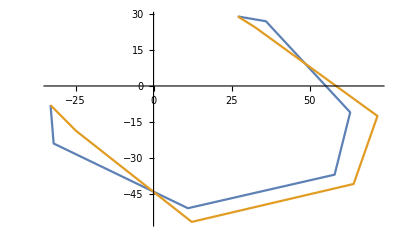

Volume calculation

Diastole volume: 485

Sistole volume:457

Vol = 14.

None  Use_Contour_Radius  None

Move by MRI: {-7.2,-15.93,-14.2,-12.25,-13.68}

Diastole and sistole contour

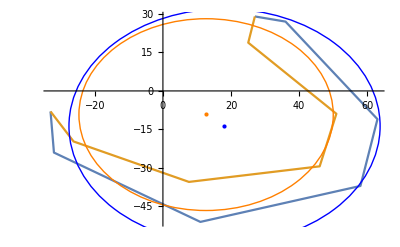

Center sphere moving = {-5.41539,4.48094}

F::HCoutourDxDyForEachChannel::Full verbouse mode

F::HCoutourDxDyForEachChannel::points of channel on contour{{-32,-24},{11,-51},{58,-37},{63,-11},{36,27}}

Function

Param model: <|a→{0.04,0.04,0.05,0.05,0.04},b→{0.02,0.02,0.025,0.025,0.02},R→{0.051,0.04,0.042,0.042,0.041},h→{0.03,0.019,0.022,0.021,0.03},x→{0,0,0,0,0},y→{0.047,0.026,0.035,0.048,0.025},hFat→{0.},flSize→{0.06,0.03}|>

Exp data: <|dZRad→{0.057,0.11,0.13,0.067,0.115},zBase→{35,33,33,30,42},flDZ→0.045,flBase→35|>

DxDy: {{-1.64375,6.83399},{5.52199,4.34891},{6.97544,0.865233},{6.10541,3.48271},{1.64375,6.83399}}

Radial Move : {0.0037,0.0022,0.0021,0.0014,0.0037}

Contours by impedance evaluation.

Diastole contour: {{-33,-8},{-32,-24},{11,-51},{58,-37},{63,-11},{36,27},{27,29}}

Sistole contour:{{-33,-8},{-29.04,-21.78},{10.5362,-48.8495},{56.2296,-35.8706},{61.6209,-10.7592},{33.04,24.78},{27,29}}

-Graphics-

Volume calculation

Diastole volume: 485

Sistole volume:396

Vol = 44.5

None  Use_Contour_Radius  FirstLayer

Move by MRI: {-7.2,-15.93,-14.2,-12.25,-13.68}

Diastole and sistole contour

-Graphics-

Center sphere moving = {-5.41539,4.48094}

F::HCoutourDxDyForEachChannel::Full verbouse mode

F::HCoutourDxDyForEachChannel::points of channel on contour{{-32,-24},{11,-51},{58,-37},{63,-11},{36,27}}

Function

Param model: <|a→{0.04,0.04,0.05,0.05,0.04},b→{0.02,0.02,0.025,0.025,0.02},R→{0.051,0.04,0.042,0.042,0.041},h→{0.03,0.019,0.022,0.021,0.03},x→{0,0,0,0,0},y→{0.047,0.026,0.035,0.048,0.025},hFat→{0.},flSize→{0.06,0.03}|>

Exp data: <|dZRad→{0.057,0.11,0.13,0.067,0.115},zBase→{35,33,33,30,42},flDZ→0.045,flBase→35|>

DxDy: {{-1.64375,6.83399},{5.52199,4.34891},{6.97544,0.865233},{6.10541,3.48271},{1.64375,6.83399}}

Radial Move : {0.0078,0.0034,0.0029,0.0024,0.0058}

Contours by impedance evaluation.

Diastole contour: {{-33,-8},{-32,-24},{11,-51},{58,-37},{63,-11},{36,27},{27,29}}

Sistole contour:{{-33,-8},{-25.76,-19.32},{10.2832,-47.6764},{55.5551,-35.4403},{60.6358,-10.5872},{31.36,23.52},{27,29}}

-Graphics-

Volume calculation

Diastole volume: 485

Sistole volume:329

Vol = 78.

None  Use_Contour_Radius  FirstLayer_CenterMove

Move by MRI: {-7.2,-15.93,-14.2,-12.25,-13.68}

Diastole and sistole contour

-Graphics-

Center sphere moving = {-5.41539,4.48094}

F::HCoutourDxDyForEachChannel::Full verbouse mode

F::HCoutourDxDyForEachChannel::points of channel on contour{{-32,-24},{11,-51},{58,-37},{63,-11},{36,27}}

verb full

dR: {0.008,0.0009,0.0005,-0.0026,0.0045}

Center move: {{-1.64375,6.83399},{5.52199,4.34891},{6.97544,0.865233},{6.10541,3.48271},{1.64375,6.83399}}

Edge move (because center move){0.0101903,-0.00437938,-0.00646642,-0.00856923,0.00350173}

Function

Param model: <|a→{0.04,0.04,0.05,0.05,0.04},b→{0.02,0.02,0.025,0.025,0.02},R→{0.051,0.04,0.042,0.042,0.041},h→{0.03,0.019,0.022,0.021,0.03},x→{0,0,0,0,0},y→{0.047,0.026,0.035,0.048,0.025},hFat→{0.},flSize→{0.06,0.03}|>

Exp data: <|dZRad→{0.057,0.11,0.13,0.067,0.115},zBase→{35,33,33,30,42},flDZ→0.045,flBase→35|>

DxDy: {{-1.64375,6.83399},{5.52199,4.34891},{6.97544,0.865233},{6.10541,3.48271},{1.64375,6.83399}}

Radial Move : {0.0101903,-0.00437938,-0.00646642,-0.00856923,0.00350173}

Contours by impedance evaluation.

Diastole contour: {{-33,-8},{-32,-24},{11,-51},{58,-37},{63,-11},{36,27},{27,29}}

Sistole contour:{{-33,-8},{-23.8478,-17.8858},{11.9233,-55.2809},{63.4516,-40.4777},{71.4415,-12.4739},{33.1986,24.899},{27,29}}

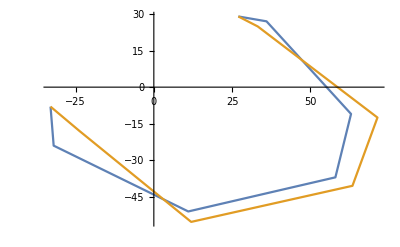

Volume calculation

Diastole volume: 485

Sistole volume:443

Vol = 21.

ValveMove  Use_Contour  None

Move by MRI: {-7.2,-15.93,-14.2,-12.25,-13.68}

Diastole and sistole contour

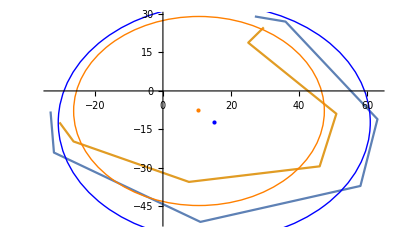

Center sphere moving = {-4.48457,4.40812}

F::HCoutourDxDyForEachChannel::Full verbouse mode

F::HCoutourDxDyForEachChannel::points of channel on contour{{-32,-24},{11,-51},{58,-37},{63,-11},{36,27}}

Function

Param model: <|a→{0.04,0.04,0.05,0.05,0.04},b→{0.02,0.02,0.025,0.025,0.02},R→{0.051,0.04,0.042,0.042,0.041},h→{0.03,0.019,0.022,0.021,0.03},x→{0,0,0,0,0},y→{0.047,0.026,0.035,0.048,0.025},hFat→{0.},flSize→{0.06,0.03}|>

Exp data: <|dZRad→{0.057,0.11,0.13,0.067,0.115},zBase→{35,33,33,30,42},flDZ→0.045,flBase→35|>

DxDy: {{-0.942783,6.21724},{5.25455,3.45436},{6.15153,1.30445},{5.17594,3.57107},{0.942783,6.21724}}

Radial Move : {0.0037,0.0022,0.0021,0.0014,0.0037}

Contours by impedance evaluation.

Diastole contour: {{-33,-8},{-32,-24},{11,-51},{58,-37},{63,-11},{36,27},{27,29}}

Sistole contour:{{-30.3756,-12.2559},{-29.04,-21.78},{10.5362,-48.8495},{56.2296,-35.8706},{61.6209,-10.7592},{33.04,24.78},{29.6244,24.7441}}

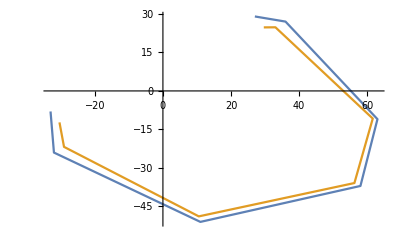

Volume calculation

Diastole volume: 485

Sistole volume:408

Vol = 38.5

ValveMove  Use_Contour  FirstLayer

Move by MRI: {-7.2,-15.93,-14.2,-12.25,-13.68}

Diastole and sistole contour

-Graphics-

Center sphere moving = {-4.48457,4.40812}

F::HCoutourDxDyForEachChannel::Full verbouse mode

F::HCoutourDxDyForEachChannel::points of channel on contour{{-32,-24},{11,-51},{58,-37},{63,-11},{36,27}}

Function

Param model: <|a→{0.04,0.04,0.05,0.05,0.04},b→{0.02,0.02,0.025,0.025,0.02},R→{0.051,0.04,0.042,0.042,0.041},h→{0.03,0.019,0.022,0.021,0.03},x→{0,0,0,0,0},y→{0.047,0.026,0.035,0.048,0.025},hFat→{0.},flSize→{0.06,0.03}|>

Exp data: <|dZRad→{0.057,0.11,0.13,0.067,0.115},zBase→{35,33,33,30,42},flDZ→0.045,flBase→35|>

DxDy: {{-0.942783,6.21724},{5.25455,3.45436},{6.15153,1.30445},{5.17594,3.57107},{0.942783,6.21724}}

Radial Move : {0.0078,0.0034,0.0029,0.0024,0.0058}

Contours by impedance evaluation.

Diastole contour: {{-33,-8},{-32,-24},{11,-51},{58,-37},{63,-11},{36,27},{27,29}}

Sistole contour:{{-30.3756,-12.2559},{-25.76,-19.32},{10.2832,-47.6764},{55.5551,-35.4403},{60.6358,-10.5872},{31.36,23.52},{29.6244,24.7441}}

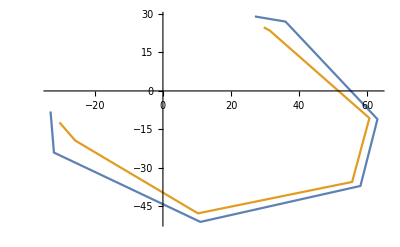

Volume calculation

Diastole volume: 485

Sistole volume:321

Vol = 82.

ValveMove  Use_Contour  FirstLayer_CenterMove

Move by MRI: {-7.2,-15.93,-14.2,-12.25,-13.68}

Diastole and sistole contour

-Graphics-

Center sphere moving = {-4.48457,4.40812}

F::HCoutourDxDyForEachChannel::Full verbouse mode

F::HCoutourDxDyForEachChannel::points of channel on contour{{-32,-24},{11,-51},{58,-37},{63,-11},{36,27}}

verb full

dR: {0.0077,0.0013,0.0009,-0.0018,0.0048}

Center move: {{-0.942783,6.21724},{5.25455,3.45436},{6.15153,1.30445},{5.17594,3.57107},{0.942783,6.21724}}

Edge move (because center move){0.00909146,-0.00380007,-0.00523082,-0.00683012,0.00439511}

Function

Param model: <|a→{0.04,0.04,0.05,0.05,0.04},b→{0.02,0.02,0.025,0.025,0.02},R→{0.051,0.04,0.042,0.042,0.041},h→{0.03,0.019,0.022,0.021,0.03},x→{0,0,0,0,0},y→{0.047,0.026,0.035,0.048,0.025},hFat→{0.},flSize→{0.06,0.03}|>

Exp data: <|dZRad→{0.057,0.11,0.13,0.067,0.115},zBase→{35,33,33,30,42},flDZ→0.045,flBase→35|>

DxDy: {{-0.942783,6.21724},{5.25455,3.45436},{6.15153,1.30445},{5.17594,3.57107},{0.942783,6.21724}}

Radial Move : {0.00909146,-0.00380007,-0.00523082,-0.00683012,0.00439511}

Contours by impedance evaluation.

Diastole contour: {{-33,-8},{-32,-24},{11,-51},{58,-37},{63,-11},{36,27},{27,29}}

Sistole contour:{{-30.3756,-12.2559},{-24.7268,-18.5451},{11.8012,-54.7146},{62.4099,-39.8132},{69.7283,-12.1748},{32.4839,24.3629},{29.6244,24.7441}}

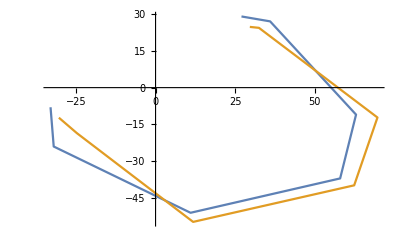

Volume calculation

Diastole volume: 485

Sistole volume:439

Vol = 23.

ValveMove  Use_Contour_Radius  None

Move by MRI: {-7.2,-15.93,-14.2,-12.25,-13.68}

Diastole and sistole contour

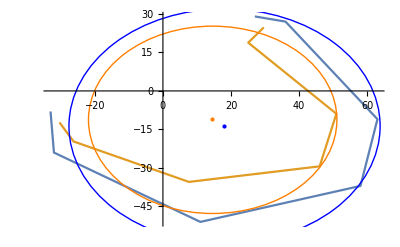

Center sphere moving = {-3.47782,2.4568}

F::HCoutourDxDyForEachChannel::Full verbouse mode

F::HCoutourDxDyForEachChannel::points of channel on contour{{-32,-24},{11,-51},{58,-37},{63,-11},{36,27}}

Function

Param model: <|a→{0.04,0.04,0.05,0.05,0.04},b→{0.02,0.02,0.025,0.025,0.02},R→{0.051,0.04,0.042,0.042,0.041},h→{0.03,0.019,0.022,0.021,0.03},x→{0,0,0,0,0},y→{0.047,0.026,0.035,0.048,0.025},hFat→{0.},flSize→{0.06,0.03}|>

Exp data: <|dZRad→{0.057,0.11,0.13,0.067,0.115},zBase→{35,33,33,30,42},flDZ→0.045,flBase→35|>

DxDy: {{-1.30818,4.05213},{3.13483,2.88166},{4.25333,0.200807},{3.84856,1.822},{1.30818,4.05213}}

Radial Move : {0.0037,0.0022,0.0021,0.0014,0.0037}

Contours by impedance evaluation.

Diastole contour: {{-33,-8},{-32,-24},{11,-51},{58,-37},{63,-11},{36,27},{27,29}}

Sistole contour:{{-30.3756,-12.2559},{-29.04,-21.78},{10.5362,-48.8495},{56.2296,-35.8706},{61.6209,-10.7592},{33.04,24.78},{29.6244,24.7441}}

-Graphics-

Volume calculation

Diastole volume: 485

Sistole volume:408

Vol = 38.5

ValveMove  Use_Contour_Radius  FirstLayer

Move by MRI: {-7.2,-15.93,-14.2,-12.25,-13.68}

Diastole and sistole contour

-Graphics-

Center sphere moving = {-3.47782,2.4568}

F::HCoutourDxDyForEachChannel::Full verbouse mode

F::HCoutourDxDyForEachChannel::points of channel on contour{{-32,-24},{11,-51},{58,-37},{63,-11},{36,27}}

Function

Param model: <|a→{0.04,0.04,0.05,0.05,0.04},b→{0.02,0.02,0.025,0.025,0.02},R→{0.051,0.04,0.042,0.042,0.041},h→{0.03,0.019,0.022,0.021,0.03},x→{0,0,0,0,0},y→{0.047,0.026,0.035,0.048,0.025},hFat→{0.},flSize→{0.06,0.03}|>

Exp data: <|dZRad→{0.057,0.11,0.13,0.067,0.115},zBase→{35,33,33,30,42},flDZ→0.045,flBase→35|>

DxDy: {{-1.30818,4.05213},{3.13483,2.88166},{4.25333,0.200807},{3.84856,1.822},{1.30818,4.05213}}

Radial Move : {0.0078,0.0034,0.0029,0.0024,0.0058}

Contours by impedance evaluation.

Diastole contour: {{-33,-8},{-32,-24},{11,-51},{58,-37},{63,-11},{36,27},{27,29}}

Sistole contour:{{-30.3756,-12.2559},{-25.76,-19.32},{10.2832,-47.6764},{55.5551,-35.4403},{60.6358,-10.5872},{31.36,23.52},{29.6244,24.7441}}

-Graphics-

Volume calculation

Diastole volume: 485

Sistole volume:321

Vol = 82.

ValveMove  Use_Contour_Radius  FirstLayer_CenterMove

Move by MRI: {-7.2,-15.93,-14.2,-12.25,-13.68}

Diastole and sistole contour

-Graphics-

Center sphere moving = {-3.47782,2.4568}

F::HCoutourDxDyForEachChannel::Full verbouse mode

F::HCoutourDxDyForEachChannel::points of channel on contour{{-32,-24},{11,-51},{58,-37},{63,-11},{36,27}}

verb full

dR: {0.0084,0.0022,0.0017,-0.0004,0.0052}

Center move: {{-1.30818,4.05213},{3.13483,2.88166},{4.25333,0.200807},{3.84856,1.822},{1.30818,4.05213}}

Edge move (because center move){0.00990134,-0.000824828,-0.00255283,-0.0042094,0.00412189}

Function

Param model: <|a→{0.04,0.04,0.05,0.05,0.04},b→{0.02,0.02,0.025,0.025,0.02},R→{0.051,0.04,0.042,0.042,0.041},h→{0.03,0.019,0.022,0.021,0.03},x→{0,0,0,0,0},y→{0.047,0.026,0.035,0.048,0.025},hFat→{0.},flSize→{0.06,0.03}|>

Exp data: <|dZRad→{0.057,0.11,0.13,0.067,0.115},zBase→{35,33,33,30,42},flDZ→0.045,flBase→35|>

DxDy: {{-1.30818,4.05213},{3.13483,2.88166},{4.25333,0.200807},{3.84856,1.822},{1.30818,4.05213}}

Radial Move : {0.00990134,-0.000824828,-0.00255283,-0.0042094,0.00412189}

Contours by impedance evaluation.

Diastole contour: {{-33,-8},{-32,-24},{11,-51},{58,-37},{63,-11},{36,27},{27,29}}

Sistole contour:{{-30.3756,-12.2559},{-24.0789,-18.0592},{11.1739,-51.8063},{60.1522,-38.3729},{67.1467,-11.724},{32.7025,24.5269},{29.6244,24.7441}}

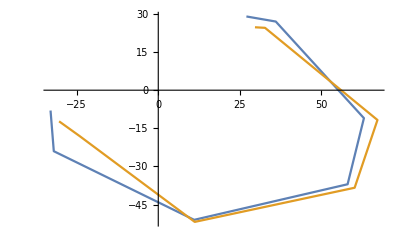

Volume calculation

Diastole volume: 485

Sistole volume:396

Vol = 44.5

```mathematica
ivan = TotalModelling["Ivan", True];
```

#### Alex

None  Use_Contour  None

Move by MRI: {-1.7,-7,-7,-9,-18}

Diastole and sistole contour

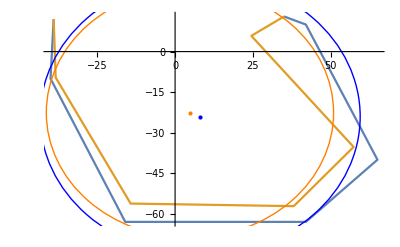

Center sphere moving = {-3.2753,1.41312}

F::HCoutourDxDyForEachChannel::Full verbouse mode

F::HCoutourDxDyForEachChannel::points of channel on contour{{-40,-10},{-16,-63},{42,-63},{65,-40},{42,10}}

Function

Param model: <|a→{0.04,0.04,0.05,0.05,0.04},b→{0.02,0.02,0.025,0.025,0.02},R→{0.055,0.05,0.042,0.05,0.055},h→{0.037,0.037,0.037,0.037,0.037},x→{0,0,0,0,0},y→{0.015,0.045,0.04,0.05,0.055},hFat→{0.013},flSize→{0.06,0.03}|>

Exp data: <|dZRad→{0.072,0.063,0.054,0.042,0.069},zBase→{95,83,73,70,108},flDZ→0.125,flBase→64|>

DxDy: {{-2.83477,2.1653},{0.563409,3.52236},{2.99259,1.94136},{3.53004,0.513082},{2.85892,2.13331}}

Radial Move : {0.0012,0.0015,0.0007,0.0007,0.0013}

Contours by impedance evaluation.

Diastole contour: {{-39,12},{-40,-10},{-16,-63},{42,-63},{65,-40},{42,10},{35,13}}

Sistole contour:{{-39,12},{-38.8358,-9.70896},{-15.6308,-61.5462},{41.6117,-62.4176},{64.4038,-39.6331},{40.7354,9.69889},{35,13}}

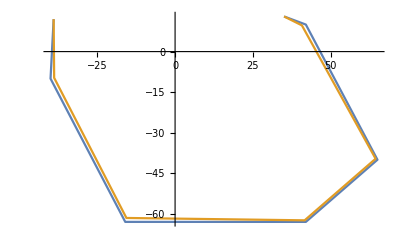

Volume calculation

Diastole volume: 604

Sistole volume:565

Vol = 19.5

None  Use_Contour  FirstLayer

Move by MRI: {-1.7,-7,-7,-9,-18}

Diastole and sistole contour

-Graphics-

Center sphere moving = {-3.2753,1.41312}

F::HCoutourDxDyForEachChannel::Full verbouse mode

F::HCoutourDxDyForEachChannel::points of channel on contour{{-40,-10},{-16,-63},{42,-63},{65,-40},{42,10}}

Function

Param model: <|a→{0.04,0.04,0.05,0.05,0.04},b→{0.02,0.02,0.025,0.025,0.02},R→{0.055,0.05,0.042,0.05,0.055},h→{0.037,0.037,0.037,0.037,0.037},x→{0,0,0,0,0},y→{0.015,0.045,0.04,0.05,0.055},hFat→{0.013},flSize→{0.06,0.03}|>

Exp data: <|dZRad→{0.072,0.063,0.054,0.042,0.069},zBase→{95,83,73,70,108},flDZ→0.125,flBase→64|>

DxDy: {{-2.83477,2.1653},{0.563409,3.52236},{2.99259,1.94136},{3.53004,0.513082},{2.85892,2.13331}}

Radial Move : {0.0042,0.0058,0.0027,0.0032,0.0049}

Contours by impedance evaluation.

Diastole contour: {{-39,12},{-40,-10},{-16,-63},{42,-63},{65,-40},{42,10},{35,13}}

Sistole contour:{{-39,12},{-35.9254,-8.98135},{-14.5723,-57.3785},{40.5023,-60.7535},{62.2747,-38.3229},{37.2332,8.86506},{35,13}}

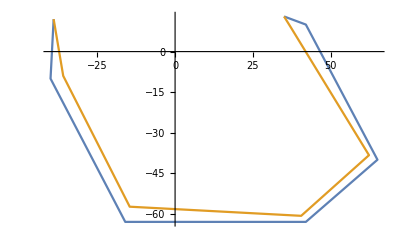

Volume calculation

Diastole volume: 604

Sistole volume:445

Vol = 79.5

None  Use_Contour  FirstLayer_CenterMove

Move by MRI: {-1.7,-7,-7,-9,-18}

Diastole and sistole contour

-Graphics-

Center sphere moving = {-3.2753,1.41312}

F::HCoutourDxDyForEachChannel::Full verbouse mode

F::HCoutourDxDyForEachChannel::points of channel on contour{{-40,-10},{-16,-63},{42,-63},{65,-40},{42,10}}

verb full

dR: {0.0043,0.0052,0.0018,0.0011,0.0021}

Center move: {{-2.83477,2.1653},{0.563409,3.52236},{2.99259,1.94136},{3.53004,0.513082},{2.85892,2.13331}}

Edge move (because center move){0.00718103,0.00477528,-0.00114569,-0.00242735,-0.000715889}

Function

Param model: <|a→{0.04,0.04,0.05,0.05,0.04},b→{0.02,0.02,0.025,0.025,0.02},R→{0.055,0.05,0.042,0.05,0.055},h→{0.037,0.037,0.037,0.037,0.037},x→{0,0,0,0,0},y→{0.015,0.045,0.04,0.05,0.055},hFat→{0.013},flSize→{0.06,0.03}|>

Exp data: <|dZRad→{0.072,0.063,0.054,0.042,0.069},zBase→{95,83,73,70,108},flDZ→0.125,flBase→64|>

DxDy: {{-2.83477,2.1653},{0.563409,3.52236},{2.99259,1.94136},{3.53004,0.513082},{2.85892,2.13331}}

Radial Move : {0.00718103,0.00477528,-0.00114569,-0.00242735,-0.000715889}

Contours by impedance evaluation.

Diastole contour: {{-39,12},{-40,-10},{-16,-63},{42,-63},{65,-40},{42,10},{35,13}}

Sistole contour:{{-39,12},{-33.0334,-8.25834},{-14.8245,-58.3717},{42.6355,-63.9533},{67.0673,-41.2722},{42.6964,10.1658},{35,13}}

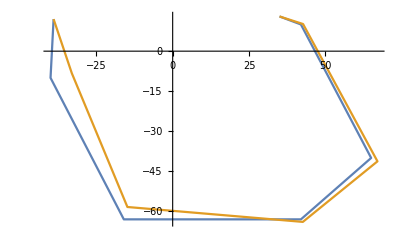

Volume calculation

Diastole volume: 604

Sistole volume:537

Vol = 33.5

None  Use_Contour_Radius  None

Move by MRI: {-1.7,-7,-7,-9,-18}

Diastole and sistole contour

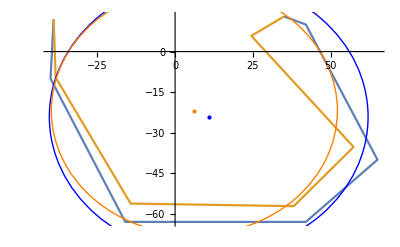

Center sphere moving = {-4.61037,2.22943}

F::HCoutourDxDyForEachChannel::Full verbouse mode

F::HCoutourDxDyForEachChannel::points of channel on contour{{-40,-10},{-16,-63},{42,-63},{65,-40},{42,10}}

Function

Param model: <|a→{0.04,0.04,0.05,0.05,0.04},b→{0.02,0.02,0.025,0.025,0.02},R→{0.055,0.05,0.042,0.05,0.055},h→{0.037,0.037,0.037,0.037,0.037},x→{0,0,0,0,0},y→{0.015,0.045,0.04,0.05,0.055},hFat→{0.013},flSize→{0.06,0.03}|>

Exp data: <|dZRad→{0.072,0.063,0.054,0.042,0.069},zBase→{95,83,73,70,108},flDZ→0.125,flBase→64|>

DxDy: {{-3.932,3.28104},{1.02597,5.0173},{4.41237,2.5994},{5.0949,0.517572},{3.96862,3.23666}}

Radial Move : {0.0012,0.0015,0.0007,0.0007,0.0013}

Contours by impedance evaluation.

Diastole contour: {{-39,12},{-40,-10},{-16,-63},{42,-63},{65,-40},{42,10},{35,13}}

Sistole contour:{{-39,12},{-38.8358,-9.70896},{-15.6308,-61.5462},{41.6117,-62.4176},{64.4038,-39.6331},{40.7354,9.69889},{35,13}}

-Graphics-

Volume calculation

Diastole volume: 604

Sistole volume:565

Vol = 19.5

None  Use_Contour_Radius  FirstLayer

Move by MRI: {-1.7,-7,-7,-9,-18}

Diastole and sistole contour

-Graphics-

Center sphere moving = {-4.61037,2.22943}

F::HCoutourDxDyForEachChannel::Full verbouse mode

F::HCoutourDxDyForEachChannel::points of channel on contour{{-40,-10},{-16,-63},{42,-63},{65,-40},{42,10}}

Function

Param model: <|a→{0.04,0.04,0.05,0.05,0.04},b→{0.02,0.02,0.025,0.025,0.02},R→{0.055,0.05,0.042,0.05,0.055},h→{0.037,0.037,0.037,0.037,0.037},x→{0,0,0,0,0},y→{0.015,0.045,0.04,0.05,0.055},hFat→{0.013},flSize→{0.06,0.03}|>

Exp data: <|dZRad→{0.072,0.063,0.054,0.042,0.069},zBase→{95,83,73,70,108},flDZ→0.125,flBase→64|>

DxDy: {{-3.932,3.28104},{1.02597,5.0173},{4.41237,2.5994},{5.0949,0.517572},{3.96862,3.23666}}

Radial Move : {0.0042,0.0058,0.0027,0.0032,0.0049}

Contours by impedance evaluation.

Diastole contour: {{-39,12},{-40,-10},{-16,-63},{42,-63},{65,-40},{42,10},{35,13}}

Sistole contour:{{-39,12},{-35.9254,-8.98135},{-14.5723,-57.3785},{40.5023,-60.7535},{62.2747,-38.3229},{37.2332,8.86506},{35,13}}

-Graphics-

Volume calculation

Diastole volume: 604

Sistole volume:445

Vol = 79.5

None  Use_Contour_Radius  FirstLayer_CenterMove

Move by MRI: {-1.7,-7,-7,-9,-18}

Diastole and sistole contour

-Graphics-

Center sphere moving = {-4.61037,2.22943}

F::HCoutourDxDyForEachChannel::Full verbouse mode

F::HCoutourDxDyForEachChannel::points of channel on contour{{-40,-10},{-16,-63},{42,-63},{65,-40},{42,10}}

verb full

dR: {0.0042,0.0047,0.0013,0.0001,0.0009}

Center move: {{-3.932,3.28104},{1.02597,5.0173},{4.41237,2.5994},{5.0949,0.517572},{3.96862,3.23666}}

Edge move (because center move){0.00823807,0.00395274,-0.00302928,-0.00499222,-0.00297171}

Function

Param model: <|a→{0.04,0.04,0.05,0.05,0.04},b→{0.02,0.02,0.025,0.025,0.02},R→{0.055,0.05,0.042,0.05,0.055},h→{0.037,0.037,0.037,0.037,0.037},x→{0,0,0,0,0},y→{0.015,0.045,0.04,0.05,0.055},hFat→{0.013},flSize→{0.06,0.03}|>

Exp data: <|dZRad→{0.072,0.063,0.054,0.042,0.069},zBase→{95,83,73,70,108},flDZ→0.125,flBase→64|>

DxDy: {{-3.932,3.28104},{1.02597,5.0173},{4.41237,2.5994},{5.0949,0.517572},{3.96862,3.23666}}

Radial Move : {0.00823807,0.00395274,-0.00302928,-0.00499222,-0.00297171}

Contours by impedance evaluation.

Diastole contour: {{-39,12},{-40,-10},{-16,-63},{42,-63},{65,-40},{42,10},{35,13}}

Sistole contour:{{-39,12},{-32.0079,-8.00197},{-15.027,-59.1689},{43.6803,-65.5205},{69.2517,-42.6164},{44.8909,10.6883},{35,13}}

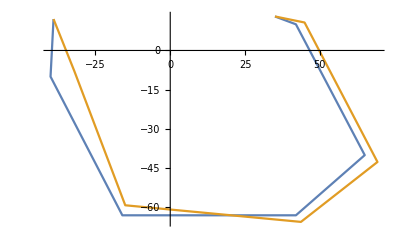

Volume calculation

Diastole volume: 604

Sistole volume:569

Vol = 17.5

ValveMove  Use_Contour  None

Move by MRI: {-1.7,-7,-7,-9,-18}

Diastole and sistole contour

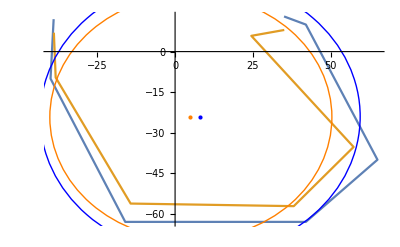

Center sphere moving = {-3.13925,-0.0508113}

F::HCoutourDxDyForEachChannel::Full verbouse mode

F::HCoutourDxDyForEachChannel::points of channel on contour{{-40,-10},{-16,-63},{42,-63},{65,-40},{42,10}}

Function

Param model: <|a→{0.04,0.04,0.05,0.05,0.04},b→{0.02,0.02,0.025,0.025,0.02},R→{0.055,0.05,0.042,0.05,0.055},h→{0.037,0.037,0.037,0.037,0.037},x→{0,0,0,0,0},y→{0.015,0.045,0.04,0.05,0.055},hFat→{0.013},flSize→{0.06,0.03}|>

Exp data: <|dZRad→{0.072,0.063,0.054,0.042,0.069},zBase→{95,83,73,70,108},flDZ→0.125,flBase→64|>

DxDy: {{-3.05785,0.712087},{-0.821987,3.03015},{1.69907,2.6402},{2.64694,1.68855},{3.06566,0.677686}}

Radial Move : {0.0012,0.0015,0.0007,0.0007,0.0013}

Contours by impedance evaluation.

Diastole contour: {{-39,12},{-40,-10},{-16,-63},{42,-63},{65,-40},{42,10},{35,13}}

Sistole contour:{{-38.9324,7.00046},{-38.8358,-9.70896},{-15.6308,-61.5462},{41.6117,-62.4176},{64.4038,-39.6331},{40.7354,9.69889},{35.0676,8.00046}}

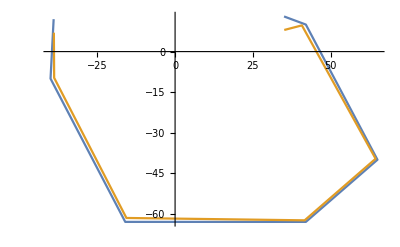

Volume calculation

Diastole volume: 604

Sistole volume:567

Vol = 18.5

ValveMove  Use_Contour  FirstLayer

Move by MRI: {-1.7,-7,-7,-9,-18}

Diastole and sistole contour

-Graphics-

Center sphere moving = {-3.13925,-0.0508113}

F::HCoutourDxDyForEachChannel::Full verbouse mode

F::HCoutourDxDyForEachChannel::points of channel on contour{{-40,-10},{-16,-63},{42,-63},{65,-40},{42,10}}

Function

Param model: <|a→{0.04,0.04,0.05,0.05,0.04},b→{0.02,0.02,0.025,0.025,0.02},R→{0.055,0.05,0.042,0.05,0.055},h→{0.037,0.037,0.037,0.037,0.037},x→{0,0,0,0,0},y→{0.015,0.045,0.04,0.05,0.055},hFat→{0.013},flSize→{0.06,0.03}|>

Exp data: <|dZRad→{0.072,0.063,0.054,0.042,0.069},zBase→{95,83,73,70,108},flDZ→0.125,flBase→64|>

DxDy: {{-3.05785,0.712087},{-0.821987,3.03015},{1.69907,2.6402},{2.64694,1.68855},{3.06566,0.677686}}

Radial Move : {0.0042,0.0058,0.0027,0.0032,0.0049}

Contours by impedance evaluation.

Diastole contour: {{-39,12},{-40,-10},{-16,-63},{42,-63},{65,-40},{42,10},{35,13}}

Sistole contour:{{-38.9324,7.00046},{-35.9254,-8.98135},{-14.5723,-57.3785},{40.5023,-60.7535},{62.2747,-38.3229},{37.2332,8.86506},{35.0676,8.00046}}

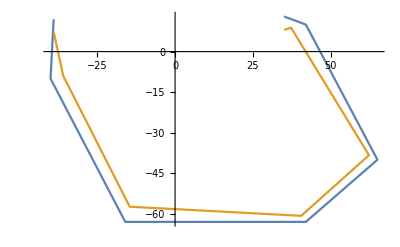

Volume calculation

Diastole volume: 604

Sistole volume:482

Vol = 61.

ValveMove  Use_Contour  FirstLayer_CenterMove

Move by MRI: {-1.7,-7,-7,-9,-18}

Diastole and sistole contour

-Graphics-

Center sphere moving = {-3.13925,-0.0508113}

F::HCoutourDxDyForEachChannel::Full verbouse mode

F::HCoutourDxDyForEachChannel::points of channel on contour{{-40,-10},{-16,-63},{42,-63},{65,-40},{42,10}}

verb full

dR: {0.0044,0.0061,0.0022,0.0016,0.002}

Center move: {{-3.05785,0.712087},{-0.821987,3.03015},{1.69907,2.6402},{2.64694,1.68855},{3.06566,0.677686}}

Edge move (because center move){0.00746286,0.00702669,0.0005886,-0.00101748,-0.00106132}

Function

Param model: <|a→{0.04,0.04,0.05,0.05,0.04},b→{0.02,0.02,0.025,0.025,0.02},R→{0.055,0.05,0.042,0.05,0.055},h→{0.037,0.037,0.037,0.037,0.037},x→{0,0,0,0,0},y→{0.015,0.045,0.04,0.05,0.055},hFat→{0.013},flSize→{0.06,0.03}|>

Exp data: <|dZRad→{0.072,0.063,0.054,0.042,0.069},zBase→{95,83,73,70,108},flDZ→0.125,flBase→64|>

DxDy: {{-3.05785,0.712087},{-0.821987,3.03015},{1.69907,2.6402},{2.64694,1.68855},{3.06566,0.677686}}

Radial Move : {0.00746286,0.00702669,0.0005886,-0.00101748,-0.00106132}

Contours by impedance evaluation.

Diastole contour: {{-39,12},{-40,-10},{-16,-63},{42,-63},{65,-40},{42,10},{35,13}}

Sistole contour:{{-38.9324,7.00046},{-32.76,-8.18999},{-14.2704,-56.1895},{41.6735,-62.5103},{65.8665,-40.5333},{43.0325,10.2458},{35.0676,8.00046}}

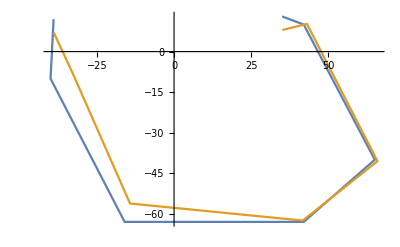

Volume calculation

Diastole volume: 604

Sistole volume:493

Vol = 55.5

ValveMove  Use_Contour_Radius  None

Move by MRI: {-1.7,-7,-7,-9,-18}

Diastole and sistole contour

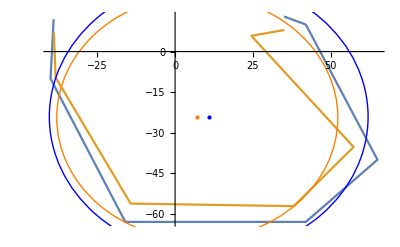

Center sphere moving = {-3.82545,-0.126138}

F::HCoutourDxDyForEachChannel::Full verbouse mode

F::HCoutourDxDyForEachChannel::points of channel on contour{{-40,-10},{-16,-63},{42,-63},{65,-40},{42,10}}

Function

Param model: <|a→{0.04,0.04,0.05,0.05,0.04},b→{0.02,0.02,0.025,0.025,0.02},R→{0.055,0.05,0.042,0.05,0.055},h→{0.037,0.037,0.037,0.037,0.037},x→{0,0,0,0,0},y→{0.015,0.045,0.04,0.05,0.055},hFat→{0.013},flSize→{0.06,0.03}|>

Exp data: <|dZRad→{0.072,0.063,0.054,0.042,0.069},zBase→{95,83,73,70,108},flDZ→0.125,flBase→64|>

DxDy: {{-3.74183,0.805437},{-1.06391,3.6767},{2.01703,3.25294},{3.19187,2.11234},{3.75064,0.763346}}

Radial Move : {0.0012,0.0015,0.0007,0.0007,0.0013}

Contours by impedance evaluation.

Diastole contour: {{-39,12},{-40,-10},{-16,-63},{42,-63},{65,-40},{42,10},{35,13}}

Sistole contour:{{-38.9324,7.00046},{-38.8358,-9.70896},{-15.6308,-61.5462},{41.6117,-62.4176},{64.4038,-39.6331},{40.7354,9.69889},{35.0676,8.00046}}

-Graphics-

Volume calculation

Diastole volume: 604

Sistole volume:567

Vol = 18.5

ValveMove  Use_Contour_Radius  FirstLayer

Move by MRI: {-1.7,-7,-7,-9,-18}

Diastole and sistole contour

-Graphics-

Center sphere moving = {-3.82545,-0.126138}

F::HCoutourDxDyForEachChannel::Full verbouse mode

F::HCoutourDxDyForEachChannel::points of channel on contour{{-40,-10},{-16,-63},{42,-63},{65,-40},{42,10}}

Function

Param model: <|a→{0.04,0.04,0.05,0.05,0.04},b→{0.02,0.02,0.025,0.025,0.02},R→{0.055,0.05,0.042,0.05,0.055},h→{0.037,0.037,0.037,0.037,0.037},x→{0,0,0,0,0},y→{0.015,0.045,0.04,0.05,0.055},hFat→{0.013},flSize→{0.06,0.03}|>

Exp data: <|dZRad→{0.072,0.063,0.054,0.042,0.069},zBase→{95,83,73,70,108},flDZ→0.125,flBase→64|>

DxDy: {{-3.74183,0.805437},{-1.06391,3.6767},{2.01703,3.25294},{3.19187,2.11234},{3.75064,0.763346}}

Radial Move : {0.0042,0.0058,0.0027,0.0032,0.0049}

Contours by impedance evaluation.

Diastole contour: {{-39,12},{-40,-10},{-16,-63},{42,-63},{65,-40},{42,10},{35,13}}

Sistole contour:{{-38.9324,7.00046},{-35.9254,-8.98135},{-14.5723,-57.3785},{40.5023,-60.7535},{62.2747,-38.3229},{37.2332,8.86506},{35.0676,8.00046}}

-Graphics-

Volume calculation

Diastole volume: 604

Sistole volume:482

Vol = 61.

ValveMove  Use_Contour_Radius  FirstLayer_CenterMove

Move by MRI: {-1.7,-7,-7,-9,-18}

Diastole and sistole contour

-Graphics-

Center sphere moving = {-3.82545,-0.126138}

F::HCoutourDxDyForEachChannel::Full verbouse mode

F::HCoutourDxDyForEachChannel::points of channel on contour{{-40,-10},{-16,-63},{42,-63},{65,-40},{42,10}}

verb full

dR: {0.0044,0.0062,0.002,0.0013,0.0013}

Center move: {{-3.74183,0.805437},{-1.06391,3.6767},{2.01703,3.25294},{3.19187,2.11234},{3.75064,0.763346}}

Edge move (because center move){0.00814824,0.0074185,0.000115463,-0.00184604,-0.00244522}

Function

Param model: <|a→{0.04,0.04,0.05,0.05,0.04},b→{0.02,0.02,0.025,0.025,0.02},R→{0.055,0.05,0.042,0.05,0.055},h→{0.037,0.037,0.037,0.037,0.037},x→{0,0,0,0,0},y→{0.015,0.045,0.04,0.05,0.055},hFat→{0.013},flSize→{0.06,0.03}|>

Exp data: <|dZRad→{0.072,0.063,0.054,0.042,0.069},zBase→{95,83,73,70,108},flDZ→0.125,flBase→64|>

DxDy: {{-3.74183,0.805437},{-1.06391,3.6767},{2.01703,3.25294},{3.19187,2.11234},{3.75064,0.763346}}

Radial Move : {0.00814824,0.0074185,0.000115463,-0.00184604,-0.00244522}

Contours by impedance evaluation.

Diastole contour: {{-39,12},{-40,-10},{-16,-63},{42,-63},{65,-40},{42,10},{35,13}}

Sistole contour:{{-38.9324,7.00046},{-32.095,-8.02376},{-14.1739,-55.8098},{41.936,-62.9039},{66.5722,-40.9675},{44.3787,10.5664},{35.0676,8.00046}}

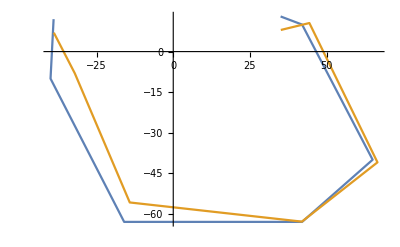

Volume calculation

Diastole volume: 604

Sistole volume:497

Vol = 53.5

```mathematica
alex = TotalModelling["Alex", True];
```

#### Artem

None  Use_Contour  None

Move by MRI: {0,-9,-15,-9.6,-5}

Diastole and sistole contour

-Graphics-

Center sphere moving = {-7.47491,5.87942}

F::HCoutourDxDyForEachChannel::Full verbouse mode

F::HCoutourDxDyForEachChannel::points of channel on contour{{-37,-27},{12,-47},{67,-42},{76,-11},{41,29}}

Function

Param model: <|a→{0.04,0.04,0.05,0.05,0.04},b→{0.02,0.02,0.025,0.025,0.02},R→{0.037,0.032,0.047,0.039,0.037},h→{0.031,0.025,0.024,0.025,0.03},x→{0,0,0,0,0},y→{0.027,0.04,0.015,0.039,0.027},hFat→{0.007},flSize→{0.06,0.03}|>

Exp data: <|dZRad→{0.04,0.055,0.11,0.083,0.076},zBase→{70,67,58,67,76},flDZ→0.1,flBase→79|>

DxDy: {{-2.57243,9.15557},{7.54584,5.7881},{9.45616,1.01137},{8.24002,4.74805},{2.70748,9.11655}}

Radial Move : {0.0005,0.0005,0.0007,0.0005,0.0009}

Contours by impedance evaluation.

Diastole contour: {{-39,-22},{-37,-27},{12,-47},{67,-42},{76,-11},{41,29},{31,32}}

Sistole contour:{{-39,-22},{-36.5961,-26.7053},{11.8763,-46.5155},{66.4069,-41.6282},{75.5052,-10.9284},{40.2652,28.4803},{31,32}}

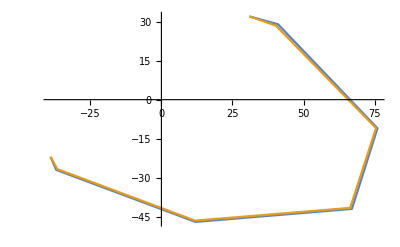

Volume calculation

Diastole volume: 622

Sistole volume:593

Vol = 14.5

None  Use_Contour  FirstLayer

Move by MRI: {0,-9,-15,-9.6,-5}

Diastole and sistole contour

-Graphics-

Center sphere moving = {-7.47491,5.87942}

F::HCoutourDxDyForEachChannel::Full verbouse mode

F::HCoutourDxDyForEachChannel::points of channel on contour{{-37,-27},{12,-47},{67,-42},{76,-11},{41,29}}

Function

Param model: <|a→{0.04,0.04,0.05,0.05,0.04},b→{0.02,0.02,0.025,0.025,0.02},R→{0.037,0.032,0.047,0.039,0.037},h→{0.031,0.025,0.024,0.025,0.03},x→{0,0,0,0,0},y→{0.027,0.04,0.015,0.039,0.027},hFat→{0.007},flSize→{0.06,0.03}|>

Exp data: <|dZRad→{0.04,0.055,0.11,0.083,0.076},zBase→{70,67,58,67,76},flDZ→0.1,flBase→79|>

DxDy: {{-2.57243,9.15557},{7.54584,5.7881},{9.45616,1.01137},{8.24002,4.74805},{2.70748,9.11655}}

Radial Move : {0.0027,0.002,0.0014,0.0012,0.0026}

Contours by impedance evaluation.

Diastole contour: {{-39,-22},{-37,-27},{12,-47},{67,-42},{76,-11},{41,29},{31,32}}

Sistole contour:{{-39,-22},{-34.819,-25.4084},{11.5052,-45.0622},{65.8138,-41.2564},{74.8124,-10.8281},{38.8773,27.4986},{31,32}}

-Graphics-

Volume calculation

Diastole volume: 622

Sistole volume:514

Vol = 54.

None  Use_Contour  FirstLayer_CenterMove

Move by MRI: {0,-9,-15,-9.6,-5}

Diastole and sistole contour

-Graphics-

Center sphere moving = {-7.47491,5.87942}

F::HCoutourDxDyForEachChannel::Full verbouse mode

F::HCoutourDxDyForEachChannel::points of channel on contour{{-37,-27},{12,-47},{67,-42},{76,-11},{41,29}}

Center move: {{-2.57243,9.15557},{7.54584,5.7881},{9.45616,1.01137},{8.24002,4.74805},{2.70748,9.11655}}

dR: {0.0014,-0.0034,0.0016,-0.0029,0.0003}

Edge move (because center move){0.00516988,-0.0104694,-0.0078449,-0.0108701,-0.00125714}

Function

Param model: <|a→{0.04,0.04,0.05,0.05,0.04},b→{0.02,0.02,0.025,0.025,0.02},R→{0.037,0.032,0.047,0.039,0.037},h→{0.031,0.025,0.024,0.025,0.03},x→{0,0,0,0,0},y→{0.027,0.04,0.015,0.039,0.027},hFat→{0.007},flSize→{0.06,0.03}|>

Exp data: <|dZRad→{0.04,0.055,0.11,0.083,0.076},zBase→{70,67,58,67,76},flDZ→0.1,flBase→79|>

DxDy: {{-2.57243,9.15557},{7.54584,5.7881},{9.45616,1.01137},{8.24002,4.74805},{2.70748,9.11655}}

Radial Move : {0.00516988,-0.0104694,-0.0078449,-0.0108701,-0.00125714}

Contours by impedance evaluation.

Diastole contour: {{-39,-22},{-37,-27},{12,-47},{67,-42},{76,-11},{41,29},{31,32}}

Sistole contour:{{-39,-22},{-32.8238,-23.9525},{14.59,-57.144},{73.6469,-46.1667},{86.758,-12.5571},{42.0263,29.726},{31,32}}

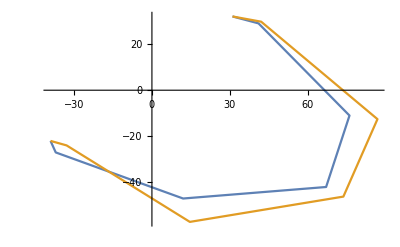

Volume calculation

Diastole volume: 622

Sistole volume:711

Vol = -44.5

None  Use_Contour_Radius  None

Move by MRI: {0,-9,-15,-9.6,-5}

Diastole and sistole contour

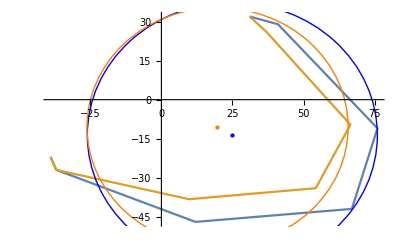

Center sphere moving = {-5.38246,3.28175}

F::HCoutourDxDyForEachChannel::Full verbouse mode

F::HCoutourDxDyForEachChannel::points of channel on contour{{-37,-27},{12,-47},{67,-42},{76,-11},{41,29}}

Function

Param model: <|a→{0.04,0.04,0.05,0.05,0.04},b→{0.02,0.02,0.025,0.025,0.02},R→{0.037,0.032,0.047,0.039,0.037},h→{0.031,0.025,0.024,0.025,0.03},x→{0,0,0,0,0},y→{0.027,0.04,0.015,0.039,0.027},hFat→{0.007},flSize→{0.06,0.03}|>

Exp data: <|dZRad→{0.04,0.055,0.11,0.083,0.076},zBase→{70,67,58,67,76},flDZ→0.1,flBase→79|>

DxDy: {{-2.41341,5.82376},{4.51128,4.40331},{6.30354,0.0782303},{5.79704,2.4769},{2.49923,5.78745}}

Radial Move : {0.0005,0.0005,0.0007,0.0005,0.0009}

Contours by impedance evaluation.

Diastole contour: {{-39,-22},{-37,-27},{12,-47},{67,-42},{76,-11},{41,29},{31,32}}

Sistole contour:{{-39,-22},{-36.5961,-26.7053},{11.8763,-46.5155},{66.4069,-41.6282},{75.5052,-10.9284},{40.2652,28.4803},{31,32}}

-Graphics-

Volume calculation

Diastole volume: 622

Sistole volume:593

Vol = 14.5

None  Use_Contour_Radius  FirstLayer

Move by MRI: {0,-9,-15,-9.6,-5}

Diastole and sistole contour

-Graphics-

Center sphere moving = {-5.38246,3.28175}

F::HCoutourDxDyForEachChannel::Full verbouse mode

F::HCoutourDxDyForEachChannel::points of channel on contour{{-37,-27},{12,-47},{67,-42},{76,-11},{41,29}}

Function

Param model: <|a→{0.04,0.04,0.05,0.05,0.04},b→{0.02,0.02,0.025,0.025,0.02},R→{0.037,0.032,0.047,0.039,0.037},h→{0.031,0.025,0.024,0.025,0.03},x→{0,0,0,0,0},y→{0.027,0.04,0.015,0.039,0.027},hFat→{0.007},flSize→{0.06,0.03}|>

Exp data: <|dZRad→{0.04,0.055,0.11,0.083,0.076},zBase→{70,67,58,67,76},flDZ→0.1,flBase→79|>

DxDy: {{-2.41341,5.82376},{4.51128,4.40331},{6.30354,0.0782303},{5.79704,2.4769},{2.49923,5.78745}}

Radial Move : {0.0027,0.002,0.0014,0.0012,0.0026}

Contours by impedance evaluation.

Diastole contour: {{-39,-22},{-37,-27},{12,-47},{67,-42},{76,-11},{41,29},{31,32}}

Sistole contour:{{-39,-22},{-34.819,-25.4084},{11.5052,-45.0622},{65.8138,-41.2564},{74.8124,-10.8281},{38.8773,27.4986},{31,32}}

-Graphics-

Volume calculation

Diastole volume: 622

Sistole volume:514

Vol = 54.

None  Use_Contour_Radius  FirstLayer_CenterMove

Move by MRI: {0,-9,-15,-9.6,-5}

Diastole and sistole contour

-Graphics-

Center sphere moving = {-5.38246,3.28175}

F::HCoutourDxDyForEachChannel::Full verbouse mode

F::HCoutourDxDyForEachChannel::points of channel on contour{{-37,-27},{12,-47},{67,-42},{76,-11},{41,29}}

Center move: {{-2.41341,5.82376},{4.51128,4.40331},{6.30354,0.0782303},{5.79704,2.4769},{2.49923,5.78745}}

dR: {0.0023,-0.001,0.0017,-0.0012,0.0014}

Edge move (because center move){0.00520561,-0.00521618,-0.00460347,-0.00692067,-0.00062565}

Function

Param model: <|a→{0.04,0.04,0.05,0.05,0.04},b→{0.02,0.02,0.025,0.025,0.02},R→{0.037,0.032,0.047,0.039,0.037},h→{0.031,0.025,0.024,0.025,0.03},x→{0,0,0,0,0},y→{0.027,0.04,0.015,0.039,0.027},hFat→{0.007},flSize→{0.06,0.03}|>

Exp data: <|dZRad→{0.04,0.055,0.11,0.083,0.076},zBase→{70,67,58,67,76},flDZ→0.1,flBase→79|>

DxDy: {{-2.41341,5.82376},{4.51128,4.40331},{6.30354,0.0782303},{5.79704,2.4769},{2.49923,5.78745}}

Radial Move : {0.00520561,-0.00521618,-0.00460347,-0.00692067,-0.00062565}

Contours by impedance evaluation.

Diastole contour: {{-39,-22},{-37,-27},{12,-47},{67,-42},{76,-11},{41,29},{31,32}}

Sistole contour:{{-39,-22},{-32.795,-23.9315},{13.2904,-52.054},{70.9005,-44.4451},{82.8493,-11.9913},{41.5108,29.3613},{31,32}}

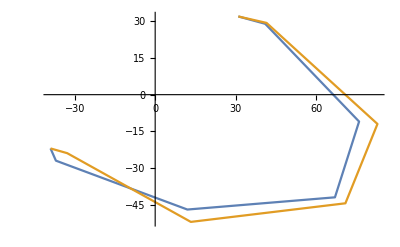

Volume calculation

Diastole volume: 622

Sistole volume:627

Vol = -2.5

ValveMove  Use_Contour  None

Move by MRI: {0,-9,-15,-9.6,-5}

Diastole and sistole contour

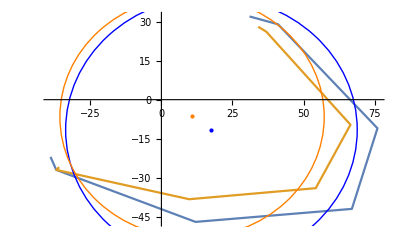

Center sphere moving = {-6.99475,5.20652}

F::HCoutourDxDyForEachChannel::Full verbouse mode

F::HCoutourDxDyForEachChannel::points of channel on contour{{-37,-27},{12,-47},{67,-42},{76,-11},{41,29}}

Function

Param model: <|a→{0.04,0.04,0.05,0.05,0.04},b→{0.02,0.02,0.025,0.025,0.02},R→{0.037,0.032,0.047,0.039,0.037},h→{0.031,0.025,0.024,0.025,0.03},x→{0,0,0,0,0},y→{0.027,0.04,0.015,0.039,0.027},hFat→{0.007},flSize→{0.06,0.03}|>

Exp data: <|dZRad→{0.04,0.055,0.11,0.083,0.076},zBase→{70,67,58,67,76},flDZ→0.1,flBase→79|>

DxDy: {{-2.58122,8.32897},{6.77507,5.48933},{8.69193,0.696255},{7.66842,4.15087},{2.70405,8.2899}}

Radial Move : {0.0005,0.0005,0.0007,0.0005,0.0009}

Contours by impedance evaluation.

Diastole contour: {{-39,-22},{-37,-27},{12,-47},{67,-42},{76,-11},{41,29},{31,32}}

Sistole contour:{{-35.946,-25.9589},{-36.5961,-26.7053},{11.8763,-46.5155},{66.4069,-41.6282},{75.5052,-10.9284},{40.2652,28.4803},{34.054,28.0411}}

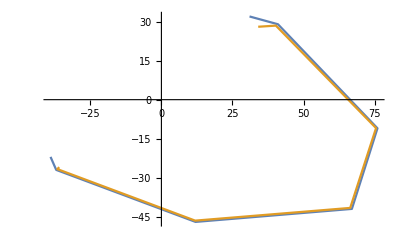

Volume calculation

Diastole volume: 622

Sistole volume:628

Vol = -3.

ValveMove  Use_Contour  FirstLayer

Move by MRI: {0,-9,-15,-9.6,-5}

Diastole and sistole contour

-Graphics-

Center sphere moving = {-6.99475,5.20652}

F::HCoutourDxDyForEachChannel::Full verbouse mode

F::HCoutourDxDyForEachChannel::points of channel on contour{{-37,-27},{12,-47},{67,-42},{76,-11},{41,29}}

Function

Param model: <|a→{0.04,0.04,0.05,0.05,0.04},b→{0.02,0.02,0.025,0.025,0.02},R→{0.037,0.032,0.047,0.039,0.037},h→{0.031,0.025,0.024,0.025,0.03},x→{0,0,0,0,0},y→{0.027,0.04,0.015,0.039,0.027},hFat→{0.007},flSize→{0.06,0.03}|>

Exp data: <|dZRad→{0.04,0.055,0.11,0.083,0.076},zBase→{70,67,58,67,76},flDZ→0.1,flBase→79|>

DxDy: {{-2.58122,8.32897},{6.77507,5.48933},{8.69193,0.696255},{7.66842,4.15087},{2.70405,8.2899}}

Radial Move : {0.0027,0.002,0.0014,0.0012,0.0026}

Contours by impedance evaluation.

Diastole contour: {{-39,-22},{-37,-27},{12,-47},{67,-42},{76,-11},{41,29},{31,32}}

Sistole contour:{{-35.946,-25.9589},{-34.819,-25.4084},{11.5052,-45.0622},{65.8138,-41.2564},{74.8124,-10.8281},{38.8773,27.4986},{34.054,28.0411}}

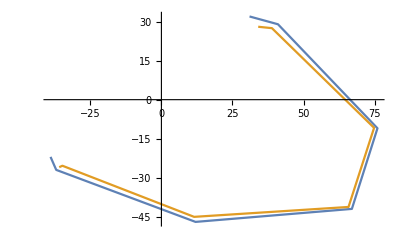

Volume calculation

Diastole volume: 622

Sistole volume:445

Vol = 88.5

ValveMove  Use_Contour  FirstLayer_CenterMove

Move by MRI: {0,-9,-15,-9.6,-5}

Diastole and sistole contour

-Graphics-

Center sphere moving = {-6.99475,5.20652}

F::HCoutourDxDyForEachChannel::Full verbouse mode

F::HCoutourDxDyForEachChannel::points of channel on contour{{-37,-27},{12,-47},{67,-42},{76,-11},{41,29}}

Center move: {{-2.58122,8.32897},{6.77507,5.48933},{8.69193,0.696255},{7.66842,4.15087},{2.70405,8.2899}}

dR: {0.0017,-0.0027,0.0017,-0.0025,0.0006}

Edge move (because center move){0.00527789,-0.00903813,-0.00698658,-0.00996031,-0.00114749}

Function

Param model: <|a→{0.04,0.04,0.05,0.05,0.04},b→{0.02,0.02,0.025,0.025,0.02},R→{0.037,0.032,0.047,0.039,0.037},h→{0.031,0.025,0.024,0.025,0.03},x→{0,0,0,0,0},y→{0.027,0.04,0.015,0.039,0.027},hFat→{0.007},flSize→{0.06,0.03}|>

Exp data: <|dZRad→{0.04,0.055,0.11,0.083,0.076},zBase→{70,67,58,67,76},flDZ→0.1,flBase→79|>

DxDy: {{-2.58122,8.32897},{6.77507,5.48933},{8.69193,0.696255},{7.66842,4.15087},{2.70405,8.2899}}

Radial Move : {0.00527789,-0.00903813,-0.00698658,-0.00996031,-0.00114749}

Contours by impedance evaluation.

Diastole contour: {{-39,-22},{-37,-27},{12,-47},{67,-42},{76,-11},{41,29},{31,32}}

Sistole contour:{{-35.946,-25.9589},{-32.7366,-23.8888},{14.2359,-55.7572},{72.9196,-45.7108},{85.8576,-12.4268},{41.9368,29.6626},{34.054,28.0411}}

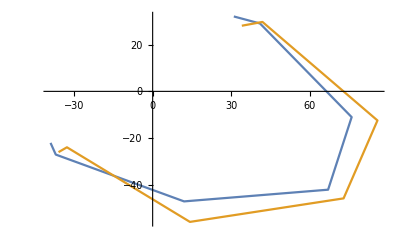

Volume calculation

Diastole volume: 622

Sistole volume:650

Vol = -14.

ValveMove  Use_Contour_Radius  None

Move by MRI: {0,-9,-15,-9.6,-5}

Diastole and sistole contour

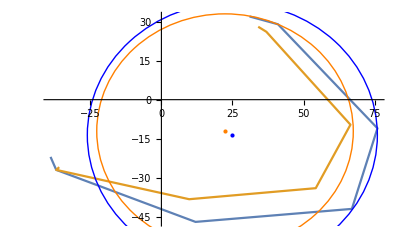

Center sphere moving = {-2.75222,1.69995}

F::HCoutourDxDyForEachChannel::Full verbouse mode

F::HCoutourDxDyForEachChannel::points of channel on contour{{-37,-27},{12,-47},{67,-42},{76,-11},{41,29}}

Function

Param model: <|a→{0.04,0.04,0.05,0.05,0.04},b→{0.02,0.02,0.025,0.025,0.02},R→{0.037,0.032,0.047,0.039,0.037},h→{0.031,0.025,0.024,0.025,0.03},x→{0,0,0,0,0},y→{0.027,0.04,0.015,0.039,0.027},hFat→{0.007},flSize→{0.06,0.03}|>

Exp data: <|dZRad→{0.04,0.055,0.11,0.083,0.076},zBase→{70,67,58,67,76},flDZ→0.1,flBase→79|>

DxDy: {{-1.22115,2.99556},{2.32797,2.24614},{3.23483,0.0214564},{2.96735,1.28818},{1.2653,2.97718}}

Radial Move : {0.0005,0.0005,0.0007,0.0005,0.0009}

Contours by impedance evaluation.

Diastole contour: {{-39,-22},{-37,-27},{12,-47},{67,-42},{76,-11},{41,29},{31,32}}

Sistole contour:{{-35.946,-25.9589},{-36.5961,-26.7053},{11.8763,-46.5155},{66.4069,-41.6282},{75.5052,-10.9284},{40.2652,28.4803},{34.054,28.0411}}

-Graphics-

Volume calculation

Diastole volume: 622

Sistole volume:628

Vol = -3.

ValveMove  Use_Contour_Radius  FirstLayer

Move by MRI: {0,-9,-15,-9.6,-5}

Diastole and sistole contour

-Graphics-

Center sphere moving = {-2.75222,1.69995}

F::HCoutourDxDyForEachChannel::Full verbouse mode

F::HCoutourDxDyForEachChannel::points of channel on contour{{-37,-27},{12,-47},{67,-42},{76,-11},{41,29}}

Function

Param model: <|a→{0.04,0.04,0.05,0.05,0.04},b→{0.02,0.02,0.025,0.025,0.02},R→{0.037,0.032,0.047,0.039,0.037},h→{0.031,0.025,0.024,0.025,0.03},x→{0,0,0,0,0},y→{0.027,0.04,0.015,0.039,0.027},hFat→{0.007},flSize→{0.06,0.03}|>

Exp data: <|dZRad→{0.04,0.055,0.11,0.083,0.076},zBase→{70,67,58,67,76},flDZ→0.1,flBase→79|>

DxDy: {{-1.22115,2.99556},{2.32797,2.24614},{3.23483,0.0214564},{2.96735,1.28818},{1.2653,2.97718}}

Radial Move : {0.0027,0.002,0.0014,0.0012,0.0026}

Contours by impedance evaluation.

Diastole contour: {{-39,-22},{-37,-27},{12,-47},{67,-42},{76,-11},{41,29},{31,32}}

Sistole contour:{{-35.946,-25.9589},{-34.819,-25.4084},{11.5052,-45.0622},{65.8138,-41.2564},{74.8124,-10.8281},{38.8773,27.4986},{34.054,28.0411}}

-Graphics-

Volume calculation

Diastole volume: 622

Sistole volume:445

Vol = 88.5

ValveMove  Use_Contour_Radius  FirstLayer_CenterMove

Move by MRI: {0,-9,-15,-9.6,-5}

Diastole and sistole contour

-Graphics-

Center sphere moving = {-2.75222,1.69995}

F::HCoutourDxDyForEachChannel::Full verbouse mode

F::HCoutourDxDyForEachChannel::points of channel on contour{{-37,-27},{12,-47},{67,-42},{76,-11},{41,29}}

Center move: {{-1.22115,2.99556},{2.32797,2.24614},{3.23483,0.0214564},{2.96735,1.28818},{1.2653,2.97718}}

dR: {0.0027,0.0007,0.0016,0.0001,0.0022}

Edge move (because center move){0.00405221,-0.00154727,-0.00163482,-0.00284601,0.00106229}

Function

Param model: <|a→{0.04,0.04,0.05,0.05,0.04},b→{0.02,0.02,0.025,0.025,0.02},R→{0.037,0.032,0.047,0.039,0.037},h→{0.031,0.025,0.024,0.025,0.03},x→{0,0,0,0,0},y→{0.027,0.04,0.015,0.039,0.027},hFat→{0.007},flSize→{0.06,0.03}|>

Exp data: <|dZRad→{0.04,0.055,0.11,0.083,0.076},zBase→{70,67,58,67,76},flDZ→0.1,flBase→79|>

DxDy: {{-1.22115,2.99556},{2.32797,2.24614},{3.23483,0.0214564},{2.96735,1.28818},{1.2653,2.97718}}

Radial Move : {0.00405221,-0.00154727,-0.00163482,-0.00284601,0.00106229}

Contours by impedance evaluation.

Diastole contour: {{-39,-22},{-37,-27},{12,-47},{67,-42},{76,-11},{41,29},{31,32}}

Sistole contour:{{-35.946,-25.9589},{-33.7267,-24.6113},{12.3828,-48.4992},{68.3852,-42.8683},{78.8167,-11.4077},{40.1327,28.3866},{34.054,28.0411}}

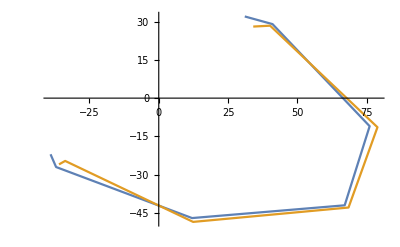

Volume calculation

Diastole volume: 622

Sistole volume:512

Vol = 55.

{{{14.5,54.,-44.5},{14.5,54.,-2.5}},{{-3.,88.5,-14.},{-3.,88.5,55.}}}

```mathematica
artem = TotalModelling["Artem", True]
```